```mathematica
(*** DATA-DRIVEN PREDICTIONS ***)
```

```mathematica
(* automation, requires defs from binomial-confidence-intervals-sesh45.nb *) 
getMonValues[dirPath_, fieldName_]:=(getValueFromListOfPairs[#,fieldName]& /@ (nameValuePairsFromFile/@(StringJoin[dirPath,"mon1_", ToString@#, "_estrate_stats.txt"]& /@ Range[2,30]) ));
```

```mathematica
(** FPR **) 
(* monitor error rates (empirical) dependency on window *)
```

```mathematica
(* automated *) 
getMonValues[dataDirPathForSeshNum[All], "FPR"]
```

{0.010586,0.001484,0.000467,0.000388,0.000271,0.000193,0.000115,0.000115,0.000114,0.000114,0.000038,0.000038,0.000038,0.000038,0.000037,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(* generated from Session 4, det1 in the data repository -- 1hz, fpr = fnr = 0.1 *) 
(* empirical - monitor FPR by window size, from mon1 (2751 frames) *) 
empFPRbyWinSizeMon1 = ListLinePlot[{{2, 0.010109} ,{3, 0.001163}, {4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}, PlotLabel->"Empirical FPR of monitor", AxesLabel->{"Monitor window size (mon1, 2.7k frames)", "FPR"}, PlotStyle->Dashing[{0.01, 0.03}]];
```

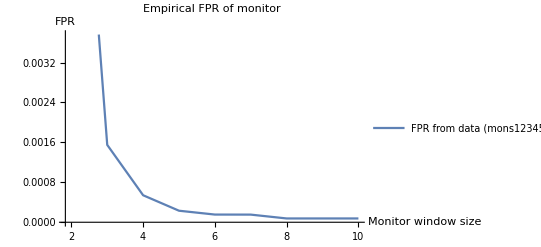

```mathematica
(* empirical - monitor FNR by window size, from mons12345 (13755 frames)  *)
empFPRbyWinSizeMons12345 = ListLinePlot[{{2, 0.010964} ,{3, 0.001550}, {4,0.000541},{5,0.000231},{6,0.000154},{7,0.000153},{8,0.000076},{9,0.000076},{10,0.000076}}, PlotLabel->"Empirical FPR of monitor", AxesLabel->{"Monitor window size", "FPR"},  PlotLegends->{"FPR from data (mons12345, 13.7k frames)"}]
```

```mathematica
(** FNR **)
```

{0.202365,0.286893,0.361722,0.4265,0.482236,0.531182,0.576592,0.617842,0.656944,0.692051,0.720733,0.748507,0.774525,0.79798,0.821043,0.83703,0.851351,0.862613,0.872236,0.881081,0.89039,0.898649,0.905405,0.914607,0.924731,0.93311,0.938053,0.934641,0.925}

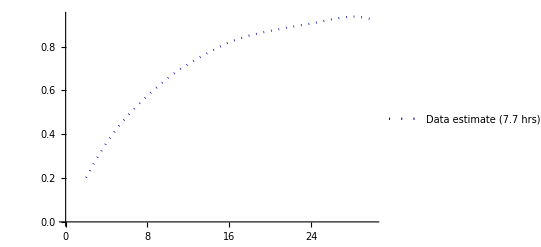

```mathematica
(* automated *) 
(* all sessions 4-7 *) 
getMonValues[dataDirPathForSeshNum[All], "FNR"]
estFNRChartSesh4567 = ListLinePlot[Inner[List, Range[2,30], getMonValues[dataDirPathForSeshNum[All], "FNR"], List], PlotStyle->{Darker@Blue,Dotted}, PlotLegends->{"Data estimate (7.7 hrs)"}]
```

{0.186486,0.266573,0.344624,0.411402,0.474277,0.529412,0.582746,0.632841,0.676357,0.716904,0.748927,0.777778,0.800481,0.820972,0.844262,0.853372,0.863924,0.869416,0.87594,0.879668,0.884259,0.890052,0.89759,0.908451,0.923729,0.93617,0.942857,0.934783,0.909091}

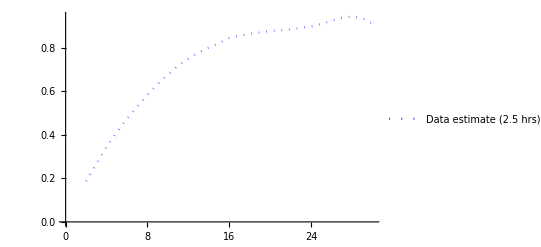

```mathematica
(* all session 6 *) 
getMonValues[dataDirPathForSeshNum[6], "FNR"]
estFNRChartSesh6= ListLinePlot[Inner[List, Range[2,30], getMonValues[dataDirPathForSeshNum[6], "FNR"], List],PlotStyle->{Lighter@Blue, Dotted}, PlotLegends->{"Data estimate (2.5 hrs)"}]
```

```mathematica
(* empirical - monitor FNR by window size, from mon1 (2751 frames)  *) 
empFNRbyWinSizeMon1 = ListLinePlot[{{2, 0.234637} ,{3, 0.327485}, {4,0.404908},{5,0.445161},{6,0.476190},{7,0.503597},{8,0.534351},{9,0.560976},{10,0.586207}}, PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from data (mon1, 2.7k frames)"}, PlotStyle->Dashing[{0.01, 0.03}]];
```

```mathematica
(* empirical  from mon2 (2751 frames)  *)
```

```mathematica
empFNRbyWinSizeMon2 = ListLinePlot[{{2, 0.162011} ,{3, 0.233918}, {4,0.300613},{5,0.367742},{6,0.428571},{7,0.489209},{8,0.534351},{9,0.585366},{10,0.629310}}, PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from data (mon2, 2.7k frames)"}, PlotStyle->Dashing[{0.01, 0.03}]];
```

```mathematica
(* empirical from mon3 (2751 frames)  *)
empFNRbyWinSizeMon3 = ListLinePlot[{{2, 0.212291} ,{3, 0.304094}, {4,0.392638},{5,0.464516},{6,0.523810},{7,0.582734},{8,0.633588},{9,0.682927},{10,0.715517}}, PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from data (mon3, 2.7k frames)"}, PlotStyle->Dashing[{0.01, 0.03}]];
```

```mathematica
(* empirical from mon4 (2751 frames)  *)
empFNRbyWinSizeMon4 = ListLinePlot[{{2, 0.234637} ,{3, 0.333333}, {4,0.398773},{5,0.470968},{6,0.544218},{7,0.597122},{8,0.648855},{9,0.691057},{10,0.724138}}, PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from data (mon4, 2.7k frames)"}, PlotStyle->Dashing[{0.01, 0.03}]];
```

```mathematica
(* empirical from mon5 (2751 frames)  *)
empFNRbyWinSizeMon5 = ListLinePlot[{{2, 0.189944} ,{3, 0.274854}, {4,0.349693},{5,0.432258},{6,0.489796},{7,0.553957},{8,0.610687},{9,0.658537},{10,0.698276}}, PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from data (mon5, 2.7k frames)"}, PlotStyle->Dashing[{0.01, 0.03}]];
```

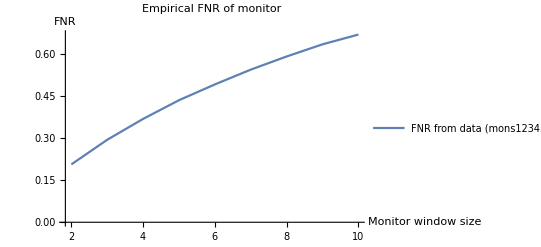

```mathematica
(* empirical - monitor FNR by window size up to window 10, from mons12345 (13755 frames)  *)
empFNRbyWinSizeMons12345UpTo10 = ListLinePlot[{{2, 0.206704} ,{3,0.294737}, {4,0.369325},{5,0.436129},{6,0.492517},{7,0.545324},{8,0.592366},{9,0.635772},{10,0.670690}}, PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from data (mons12345, 13.7k frames)"}]
```

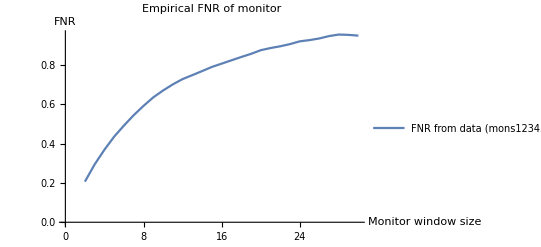

```mathematica
(* empirical - monitor FNR by window size up to window 30, from mons12345 (13755 frames)  *)
empFNRbyWinSizeMons12345UpTo30 = ListLinePlot[{{2, 0.206704} ,{3, 0.294737}, {4,0.369325},{5,0.436129},{6,0.492517},{7,0.545324},{8,0.592366},{9,0.635772},{10,0.670690}, {11,0.701818}, {12,0.728846},{13,0.748980},{14,0.769565},{15,0.790698},{16,0.807500},{17,0.824324},{18,0.841176},{19,0.857143},{20,0.875862},{21,0.886792},{22,0.895833},{23,0.906977},{24,0.921053},{25,0.927273},{26,0.935714},{27,0.947826},{28,0.955556},{29,0.953846},{30,0.950000}}, PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from data (mons12345, 13.7k frames)"}]
```

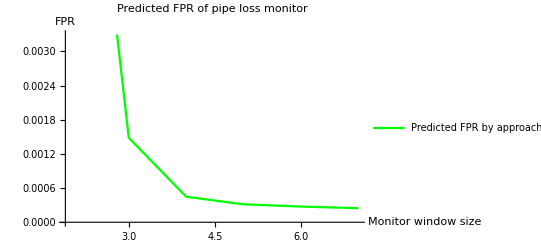

```mathematica
(*** APPROACH PREDICTIONS ***)


(* FPR/FNR estimates based on iter12345&det12345, priors/conditionals are from priorcond_iter12345_win6_stats.txt*) predFPRbyModSize = ListLinePlot[{{1, 0.010340023070913059} ,{2, 0.001483774261742787}, {3,0.00044828540282684716},{4,0.00031501632612945194},{5,0},{6,0},{7,0},{8,0},{9,0}, {10,0}}, PlotLabel->"Predicted FPR of monitor (FPR", AxesLabel->{"Modality window size", "FPR"},  PlotStyle->Green, PlotLegends->{"Predicted FPR by approach"}];
predFPRbyWinSize = ListLinePlot[{{2, 0.010340023070913059} ,{3, 0.001483774261742787}, {4,0.00044828540282684716},{5,0.00031501632612945194},{6,0.00027563453619774763},{7,0.00024669065927919963}(*,{8,0},{9,0},{10,0}*)}, PlotLabel->"Predicted FPR of pipe loss monitor", AxesLabel->{"Monitor window size", "FPR"},  PlotStyle->Green, PlotLegends->{"Predicted FPR by approach"}]
```

```mathematica
(* predicted - monitor FNR with modality size, cheaty *) 
betaERS := 1 - (1-alphaPI)(1 - alphaPI - pNChoPI)^d;
```

```mathematica
predFNRbyModSize = ListLinePlot[Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , d == #}, {#, Simplify@betaERS}]& /@ Table[n, {n,1, 9, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor size - 1", AxesLabel -> {"Modality size (= monwin size - 1)", "Monitor FNR"},PlotStyle->Magenta];
```

```mathematica
(* predicted - monitor FNR with monitor window size, cheaty *) 
betaERSmonwin := 1 - (1-alphaPI)(1 - alphaPI - pNChoPI)^(monwin-1);
```

```mathematica
predFNRbyWinSizeCheatUpTo10 =ListLinePlot[Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor window size, cheaty", AxesLabel -> {"Mon win size", "Monitor FNR"}, PlotStyle->Magenta, PlotLegends->{"FNR from cheaty prediction"}];
```

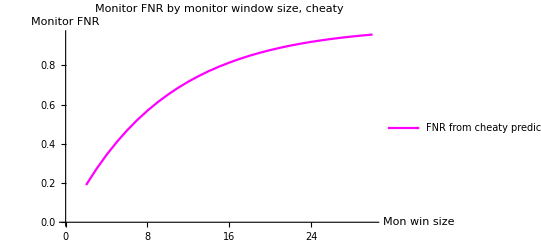

```mathematica
predFNRbyWinSizeCheatUpTo30 =ListLinePlot[Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,30, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor window size, cheaty", AxesLabel -> {"Mon win size", "Monitor FNR"}, PlotStyle->Magenta, PlotLegends->{"FNR from cheaty prediction"}]
```

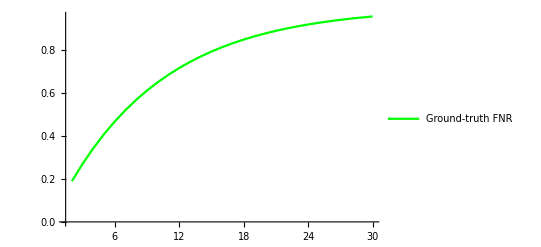

```mathematica
(* updated *) 
gtFNRChart =ListLinePlot[Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,30, 1}], (* this is mon win - 1 *)
PlotStyle->Green, PlotLegends->{"Ground-truth FNR"}, PlotRange->All]
```

```mathematica
(** realistic predictions on individual detectors, iter12345 **) 

(* on det1 fpr *) 
predFNRbyWinSizeRealDet1 = ListLinePlot[Assuming[{alphaPI==0.125000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* on det2 fpr *) 
predFNRbyWinSizeRealDet2 = ListLinePlot[Assuming[{alphaPI==0.080000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* on det3 fpr *) 
predFNRbyWinSizeRealDet3 = ListLinePlot[Assuming[{alphaPI==0.120000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* on det4 fpr *) 
predFNRbyWinSizeRealDet4 = ListLinePlot[Assuming[{alphaPI==0.135000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* on det5 fpr *) 
predFNRbyWinSizeRealDet5= ListLinePlot[Assuming[{alphaPI==0.090000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* realistic prediction on aggregate detector FPR, det 12345, iter12345 *)
predFNRbyWinSizeRealUpTo10 =ListLinePlot[Assuming[{alphaPI==0.11 , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor size, based on det12345, iter12345", AxesLabel -> {"Mon win size", "Monitor FNR"}, PlotStyle->Green, PlotLegends->{"FNR from realistic prediction"}];
```

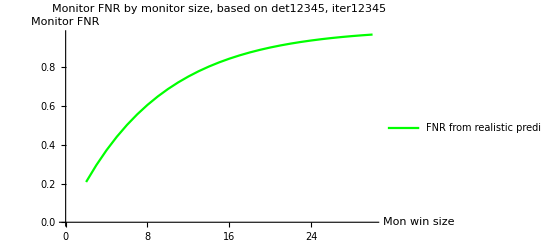

```mathematica
(* realistic prediction on aggregate detector FNR, det 12345, iter12345 *)
predFNRbyWinSizeRealUpTo30 =ListLinePlot[Assuming[{alphaPI==0.11 , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,30, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor size, based on det12345, iter12345", AxesLabel -> {"Mon win size", "Monitor FNR"}, PlotStyle->Green, PlotLegends->{"FNR from realistic prediction"}]
```

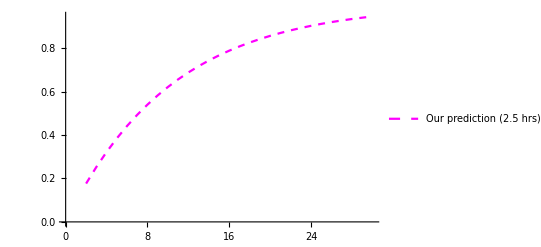

```mathematica
(* automated for session 6, det fpr 0.092478 *) 
predFNRchartSesh6 = ListLinePlot[Inner[List, Range[2,30], predFNR[countFromFiles[ "FPcount",detFilenames[fullTripleList[{6}]]]/countFromFiles[ "h0count",detFilenames[fullTripleList[{6}]]],#]&/@ Range[2,30], List], PlotStyle->{Magenta,Dashed}, PlotLegends->{"Our prediction (2.5 hrs)"}]
```

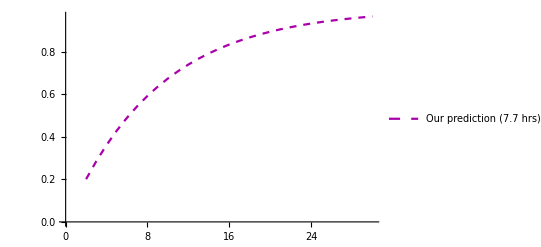

```mathematica
(* automated for sessions 4-7, det fpr 0.106042296 *) 
predFNRchartSesh4567 = ListLinePlot[Inner[List, Range[2,30], predFNR[countFromFiles[ "FPcount",detFilenames[fullTripleList[{4,5,6,7}]]]/countFromFiles[ "h0count",detFilenames[fullTripleList[{4,5,6,7}]]],#]&/@ Range[2,30], List], PlotStyle->{Darker@Magenta,Dashed}, PlotLegends->{"Our prediction (7.7 hrs)"}]
```

```mathematica
(*** VISUAL COMBINATIONS ***) 
(* combination of estimated and predicted FPR by win size, up to 10 on one and 5 on another*) 
Show[empFPRbyWinSizeMons12345,   predFPRbyWinSize, PlotLabel->"Empirical and predicted FPR of pipe loss monitor"]
```

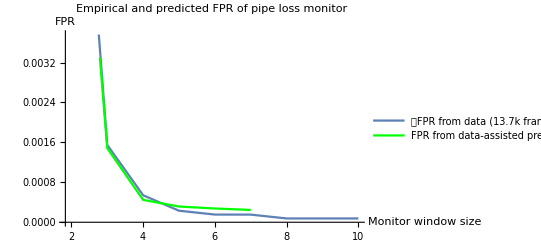

```mathematica
(* combination of estimated and predicted FNR by win size *) 
Show[empFNRbyWinSizeMons12345UpTo10, predFNRbyWinSizeCheatUpTo10, predFNRbyWinSizeRealUpTo10, PlotLabel->"Empirical and predicted FNR of pipe loss monitor, up to win of 10"]
```

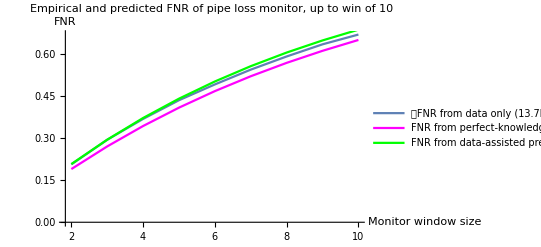

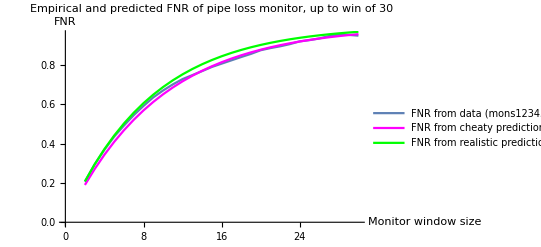

```mathematica
(* same as above for up to win = 30 *) 
Show[empFNRbyWinSizeMons12345UpTo30, predFNRbyWinSizeCheatUpTo30, predFNRbyWinSizeRealUpTo30, PlotLabel->"Empirical and predicted FNR of pipe loss monitor, up to win of 30"]
```

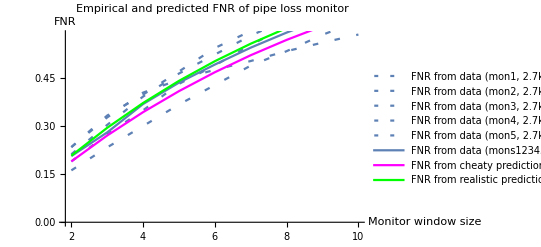

```mathematica
(* with individual empirical predictions *) 
Show[ empFNRbyWinSizeMon1, empFNRbyWinSizeMon2,  empFNRbyWinSizeMon3,empFNRbyWinSizeMon4, empFNRbyWinSizeMon5, empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

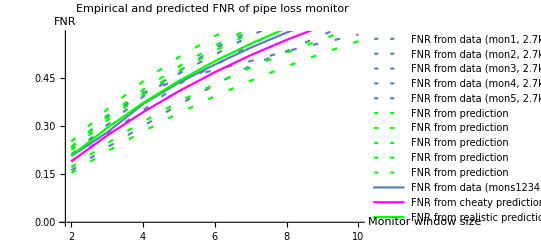

```mathematica
(* with individual theoretica predictions *) 
Show[ empFNRbyWinSizeMon1, empFNRbyWinSizeMon2,  empFNRbyWinSizeMon3,empFNRbyWinSizeMon4, empFNRbyWinSizeMon5,predFNRbyWinSizeRealDet1, predFNRbyWinSizeRealDet2,  predFNRbyWinSizeRealDet3,predFNRbyWinSizeRealDet4, predFNRbyWinSizeRealDet5, empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

```mathematica
(* all together *) 
Show[ predFNRbyWinSizeRealDet1, predFNRbyWinSizeRealDet2,  predFNRbyWinSizeRealDet3,predFNRbyWinSizeRealDet4, predFNRbyWinSizeRealDet5, empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
(*** PAIRWISE COMPARISONS OF PREDICTED AND EMPIRICAL FNRs ***)
```

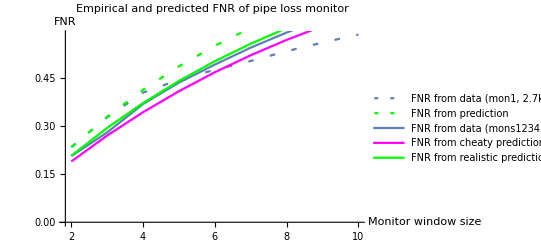

```mathematica
Show[ empFNRbyWinSizeMon1, predFNRbyWinSizeRealDet1,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

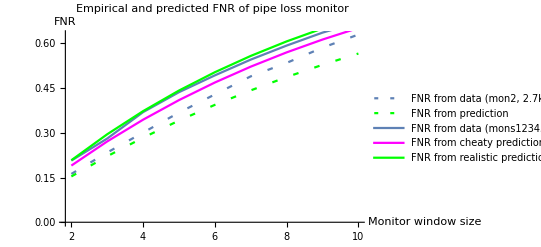

```mathematica
Show[ empFNRbyWinSizeMon2, predFNRbyWinSizeRealDet2,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

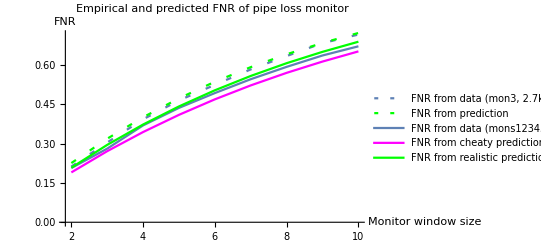

```mathematica
Show[ empFNRbyWinSizeMon3, predFNRbyWinSizeRealDet3,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

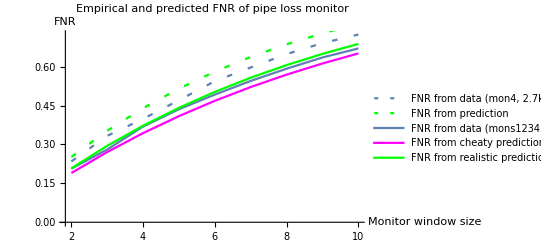

```mathematica
Show[ empFNRbyWinSizeMon4, predFNRbyWinSizeRealDet4,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

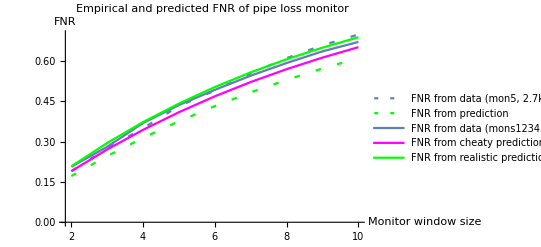

```mathematica
Show[ empFNRbyWinSizeMon5, predFNRbyWinSizeRealDet5,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

```mathematica
(*** crossover point details: ***)
```

```mathematica
(* mon1 data: *) {{5,0.445161}, {6,0.476190},{7,0.503597}};
```

```mathematica
(* mons12345 data: *) 
mons12345vals = {{2, 0.206704} ,{3, 0.280702}, {4,0.369325},{5,0.436129},{6,0.492517},{7,0.545324},{8,0.592366},{9,0.635772},{10,0.670690}}
```

{{2,0.206704},{3,0.280702},{4,0.369325},{5,0.436129},{6,0.492517},{7,0.545324},{8,0.592366},{9,0.635772},{10,0.67069}}

```mathematica
(* cheaty prediction: *)cheatyPredVals = Assuming[{alphaPI==0.1 (* cheating a bit with alpha *) , pNChoPI==0 , monwin== #},  {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}]
```

{{2,0.19},{3,0.271},{4,0.3439},{5,0.40951},{6,0.468559},{7,0.521703},{8,0.569533},{9,0.61258},{10,0.651322}}

```mathematica
(* realistic prediction *) 
realPredVals = Assuming[{alphaPI==0.11 (* from estimates det 1-5, iter 1-5 *) , pNChoPI==0 , monwin== #},  {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}]
```

{{2,0.2079},{3,0.295031},{4,0.372578},{5,0.441594},{6,0.503019},{7,0.557687},{8,0.606341},{9,0.649644},{10,0.688183}}

```mathematica
#[[2]]&  /@Abs[mons12345vals - cheatyPredVals]
```

{0.016704,0.009702,0.025425,0.026619,0.023958,0.0236209,0.0228332,0.0231925,0.0193684}

```mathematica
#[[2]]&  /@Abs[mons12345vals - realPredVals]
```

{0.001196,0.014329,0.00325259,0.00546506,0.0105017,0.0123627,0.0139751,0.0138716,0.0174928}

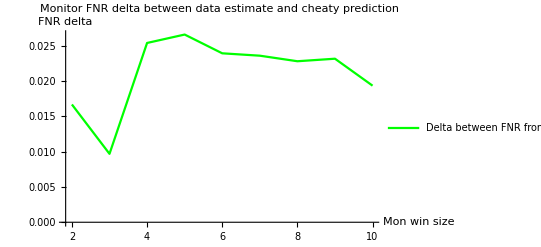

```mathematica
ListLinePlot[Transpose[{Table[n,{n,2,10,1}],#[[2]]&  /@Abs[mons12345vals - cheatyPredVals]}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR delta between data estimate and cheaty prediction", AxesLabel -> {"Mon win size", "FNR delta"}, PlotStyle->Green, PlotLegends->{"Delta between FNR from mons12345 and cheaty prediction"}]
```

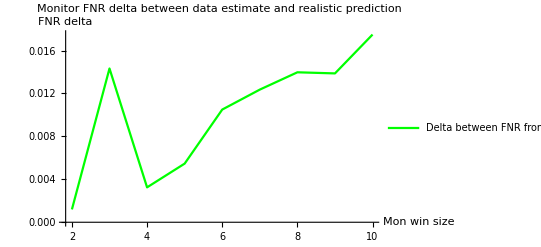

```mathematica
ListLinePlot[Transpose[{Table[n,{n,2,10,1}],#[[2]]&  /@Abs[mons12345vals - realPredVals]}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR delta between data estimate and realistic prediction", AxesLabel -> {"Mon win size", "FNR delta"}, PlotStyle->Green, PlotLegends->{"Delta between FNR from mons12345 and realistic prediction"}]
```

```mathematica
(*** Confidence intervals ***) 
(* for detector FPR for iter 1-5. Using normal distribution assumption over the probability *)
```

```mathematica
ciWidth = 1.96/n * Sqrt[ns*nf/n]
```

(1.96 √((nf ns)/n))/n

```mathematica
(* width of PI alpha confidence interval for iter12345 *) 
Assuming[{n==1000 , ns==110 , nf== n-ns},  Simplify@ciWidth]
```

0.0193931

```mathematica
(* confidence intervals for iter12345, iter1, iter2, iter3, iter4, iter5 *) 
confInterPiAlpha = Assuming[{n==#1 , ns==#2 , nf== n-ns},  Interval[{Simplify[ns/n - ciWidth], Simplify[ns/n + ciWidth]}]]& @@@{{1000,110}, {200, 25}, {200, 16}, {200, 24}, {200, 27}, {200, 18}}
```

{Interval[{0.0906069,0.129393}],Interval[{0.0791647,0.170835}],Interval[{0.0424007,0.117599}],Interval[{0.0749626,0.165037}],Interval[{0.0876395,0.18236}],Interval[{0.0503372,0.129663}]}

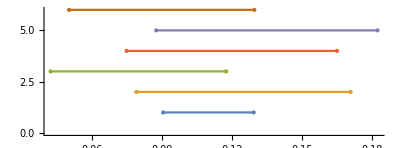

```mathematica
NumberLinePlot[confInterPiAlpha, PlotLegends->{iter12345, iter1, iter2, iter3, iter4, iter5}]
```

```mathematica
(* for FNR of PI though, the numbers are much bigger across iter 1-5 --- much tighter, 0.3% each way *) 
Assuming[{n==#1 , ns==#2 , nf== n-ns},  Interval[{Simplify[ns/n - ciWidth], Simplify[ns/n + ciWidth]}]]& @@@{{12755,1256}}
```

{Interval[{0.0933004,0.103642}]}

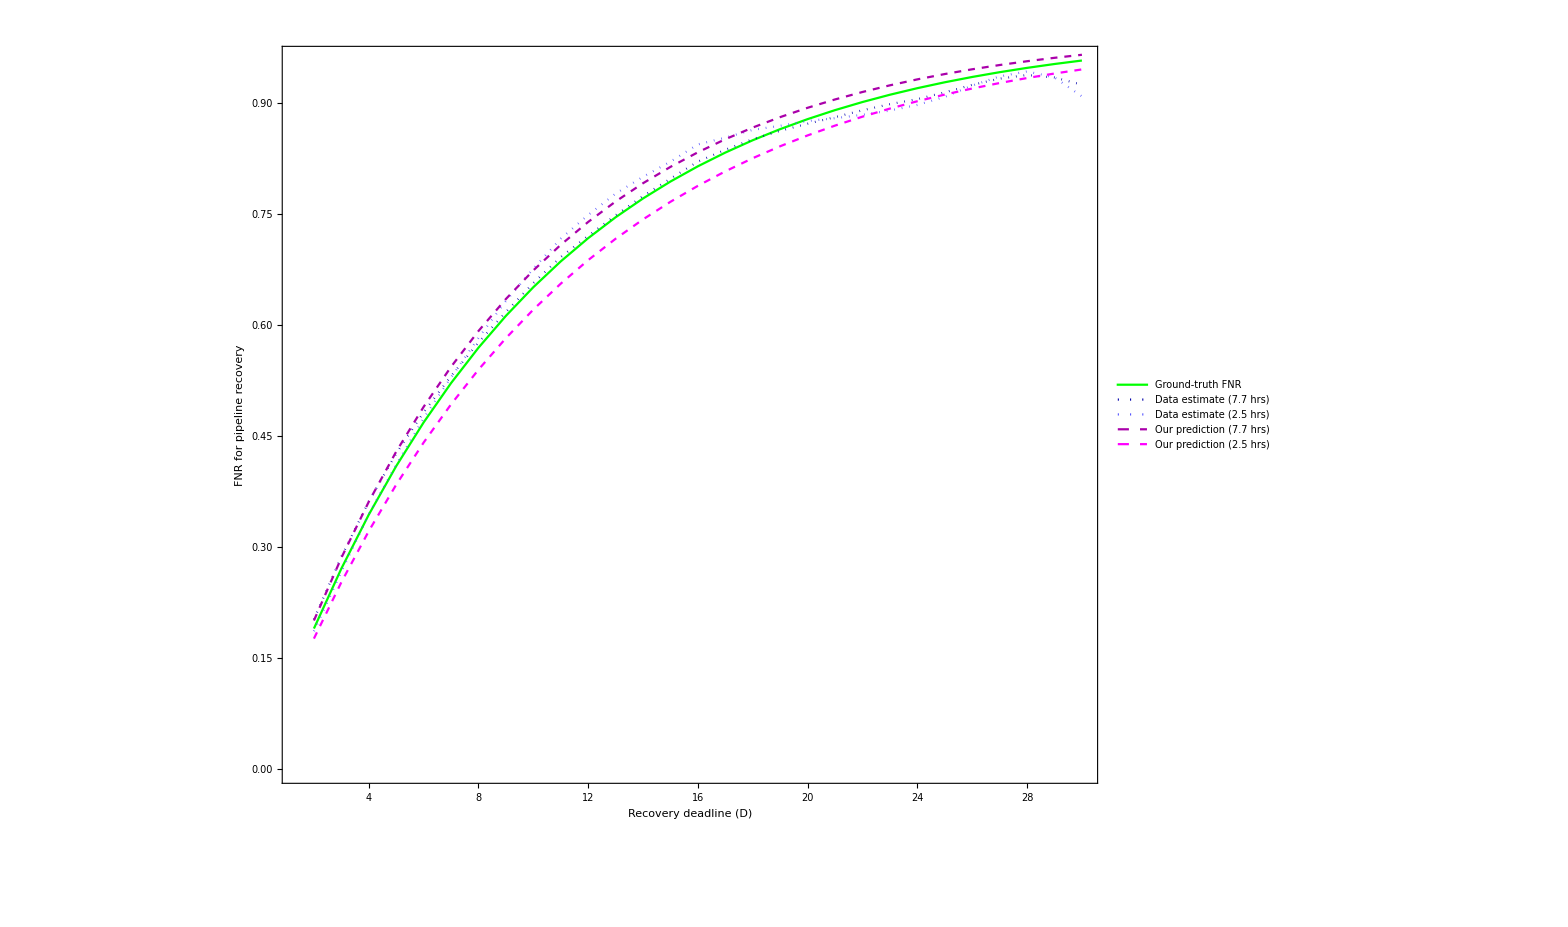

```mathematica
Show[gtFNRChart,estFNRChartSesh4567, estFNRChartSesh6, predFNRchartSesh4567, predFNRchartSesh6,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FNR"}*)Frame->True, FrameLabel->{StringJoin["Recovery deadline ", ToString[ Style["(D)", Italic], StandardForm] ],"FNR for pipeline recovery"}, ImageSize->1500, BaseStyle-> {FontSize->15}]
```

```mathematica
Export["~/graph.png",%744, ImageSize->2400] ;(* requires image size to be set *)
```